## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T

```mathematica
(*The potential is V(x). Its support is [a,b]. We assume that m=hbar=1. c defines the interval for solving the Scoedinger equation*)
```

```mathematica
V[x_]:=1/Cosh[x]^2;
a=-10;
b=10;
c=4;
```

```mathematica
(*Here we solve the Schroedinger equation assuming that to the right of the potential (x>b) we have the outgoing wave of unit flux*)
```

```mathematica
SchrEq[k0_]:=Module[{k=k0},
NDSolve[{-f''[x]/2+V[x]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}]];
```

```mathematica
(*Here we find the wave function to the left of the potential (x<a). This is done by fitting the solution of the Schroedinger equation using the Exp[\pm ISqrt[2] k x] basis. step determines the number of points used for fitting. Note that we can find the wave function also by numerical differentiation.*)
```

```mathematica
step=1;
WaveFuncLeft[k0_]:=Module[{help=SchrEq[k0]},Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k0,a,step/k0}],{Exp[I Sqrt[2]k0 x],Exp[-I Sqrt[2]k0 x]},x]];
```

```mathematica
(*Here we find the transmission coefficient -- it is determined by the coefficient in front of the incoming wave*)
```

```mathematica
T[k_]:=1/(WaveFuncLeft[k][[2]]/.x->0);
```

```mathematica
(*Now we check the solution using the exact result*)
```

```mathematica
t=Table[{k,Abs[T[k]]^2},{k,0.001,2,0.05}];
lp=ListPlot[t,PlotRange->All];
```

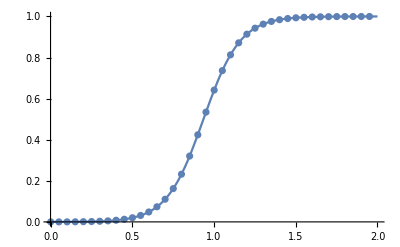

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

# Calculate T (second method)

```mathematica
V1[x_]:=1/Cosh[x]^2;
a1=-5;
b1=5;
c1=0.5;
```

```mathematica
SchrEq1[k0_]:=Module[{k=k0},
NDSolve[{-f''[x]/2+V1[x]f[x]-k^2 f[x]==0,f[b1]==Exp[I Sqrt[2]k b1],f'[b1]==I Sqrt[2] k Exp[I Sqrt[2] k b1]},f,{x,a1-c1,b1}]];
```

```mathematica
(*here we find the transmission coefficient from two points*)
T1[k0_]:=Module[{help=SchrEq1[k0]},(Exp[2Sqrt[2]I k0 a1]-Exp[2Sqrt[2]I k0 (a1-c1)])/(Exp[Sqrt[2]I k0 a1](f[a1]/.help)-Exp[Sqrt[2]I k0(a1-c1)](f[a1-c1]/.help))][[1]];
```

```mathematica
t1=Table[{k,Abs[T1[k]]^2},{k,0.001,2,0.05}];
lp1=ListPlot[t1,PlotRange->All];
```

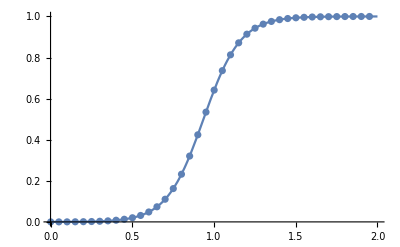

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp1]
```

## Comparing two methods

```mathematica
(*second method*)
```

```mathematica
Timing[Table[{k,Abs[T1[k]]^2},{k,0.001,2,0.01}]]
```

{0.241406,{{0.001,1.94358×10^-8},{0.011,2.35356×10^-6},{0.021,8.59561×10^-6},{0.031,0.0000187941},{0.041,0.0000330284},{0.051,0.0000514091},{0.061,0.0000740791},{0.071,0.000101215},{0.081,0.000133028},{0.091,0.000169766},{0.101,0.000211715},{0.111,0.000259203},{0.121,0.000312599},{0.131,0.000372321},{0.141,0.000438836},{0.151,0.000512663},{0.161,0.000594379},{0.171,0.000684624},{0.181,0.000784105},{0.191,0.0008936},{0.201,0.00101397},{0.211,0.00114615},{0.221,0.00129118},{0.231,0.00145019},{0.241,0.00162444},{0.251,0.00181527},{0.261,0.00202419},{0.271,0.00225283},{0.281,0.00250297},{0.291,0.00277656},{0.301,0.00307572},{0.311,0.00340279},{0.321,0.00376029},{0.331,0.004151},{0.341,0.00457793},{0.351,0.00504436},{0.361,0.00555388},{0.371,0.00611037},{0.381,0.00671808},{0.391,0.00738163},{0.401,0.00810602},{0.411,0.00889671},{0.421,0.0097596},{0.431,0.0107011},{0.441,0.0117282},{0.451,0.0128485},{0.461,0.01407},{0.471,0.0154017},{0.481,0.0168531},{0.491,0.0184345},{0.501,0.0201571},{0.511,0.0220328},{0.521,0.0240745},{0.531,0.0262962},{0.541,0.0287127},{0.551,0.0313398},{0.561,0.0341947},{0.571,0.0372955},{0.581,0.0406614},{0.591,0.0443131},{0.601,0.0482721},{0.611,0.0525614},{0.621,0.057205},{0.631,0.062228},{0.641,0.0676567},{0.651,0.0735181},{0.661,0.0798403},{0.671,0.0866519},{0.681,0.0939819},{0.691,0.10186},{0.701,0.110314},{0.711,0.119375},{0.721,0.129069},{0.731,0.139423},{0.741,0.150461},{0.751,0.162207},{0.761,0.174679},{0.771,0.187892},{0.781,0.201859},{0.791,0.216586},{0.801,0.232072},{0.811,0.248314},{0.821,0.265297},{0.831,0.283003},{0.841,0.301404},{0.851,0.320466},{0.861,0.340143},{0.871,0.360387},{0.881,0.381137},{0.891,0.402328},{0.901,0.423888},{0.911,0.445739},{0.921,0.4678},{0.931,0.489985},{0.941,0.512208},{0.951,0.53438},{0.961,0.556415},{0.971,0.578228},{0.981,0.599738},{0.991,0.620868},{1.001,0.641548},{1.011,0.661714},{1.021,0.681307},{1.031,0.700279},{1.041,0.718587},{1.051,0.736198},{1.061,0.753085},{1.071,0.76923},{1.081,0.784622},{1.091,0.799255},{1.101,0.813131},{1.111,0.826258},{1.121,0.838645},{1.131,0.850311},{1.141,0.861273},{1.151,0.871554},{1.161,0.881179},{1.171,0.890174},{1.181,0.898567},{1.191,0.906387},{1.201,0.913662},{1.211,0.920421},{1.221,0.926694},{1.231,0.932509},{1.241,0.937893},{1.251,0.942874},{1.261,0.947478},{1.271,0.95173},{1.281,0.955653},{1.291,0.95927},{1.301,0.962604},{1.311,0.965675},{1.321,0.968501},{1.331,0.971101},{1.341,0.973492},{1.351,0.97569},{1.361,0.977709},{1.371,0.979564},{1.381,0.981267},{1.391,0.982831},{1.401,0.984265},{1.411,0.985582},{1.421,0.98679},{1.431,0.987897},{1.441,0.988913},{1.451,0.989844},{1.461,0.990698},{1.471,0.991481},{1.481,0.992198},{1.491,0.992855},{1.501,0.993457},{1.511,0.994009},{1.521,0.994515},{1.531,0.994978},{1.541,0.995402},{1.551,0.995791},{1.561,0.996146},{1.571,0.996472},{1.581,0.996771},{1.591,0.997044},{1.601,0.997294},{1.611,0.997523},{1.621,0.997732},{1.631,0.997924},{1.641,0.9981},{1.651,0.99826},{1.661,0.998407},{1.671,0.998542},{1.681,0.998665},{1.691,0.998777},{1.701,0.99888},{1.711,0.998975},{1.721,0.999061},{1.731,0.99914},{1.741,0.999212},{1.751,0.999278},{1.761,0.999338},{1.771,0.999393},{1.781,0.999444},{1.791,0.99949},{1.801,0.999532},{1.811,0.999571},{1.821,0.999606},{1.831,0.999639},{1.841,0.999668},{1.851,0.999695},{1.861,0.99972},{1.871,0.999742},{1.881,0.999763},{1.891,0.999782},{1.901,0.9998},{1.911,0.999816},{1.921,0.99983},{1.931,0.999844},{1.941,0.999856},{1.951,0.999867},{1.961,0.999877},{1.971,0.999887},{1.981,0.999895},{1.991,0.999903}}}

```mathematica
(*first method*)
Timing[Table[{k,Abs[T[k]]^2},{k,0.001,2,0.01}]]
```

{0.339845,{{0.001,1.9381×10^-8},{0.011,2.34695×10^-6},{0.021,8.57174×10^-6},{0.031,0.0000187428},{0.041,0.0000329402},{0.051,0.0000512758},{0.061,0.000073894},{0.071,0.000100973},{0.081,0.000132726},{0.091,0.000169402},{0.101,0.000211292},{0.111,0.000258723},{0.121,0.00031207},{0.131,0.000371751},{0.141,0.000438236},{0.151,0.000512048},{0.161,0.000593766},{0.171,0.000684032},{0.181,0.000783554},{0.191,0.000893113},{0.201,0.00101357},{0.211,0.00114586},{0.221,0.00129103},{0.231,0.0014502},{0.241,0.00162463},{0.251,0.00181568},{0.261,0.00202482},{0.271,0.0022537},{0.281,0.00250409},{0.291,0.00277794},{0.301,0.00307737},{0.311,0.00340469},{0.321,0.00376244},{0.331,0.00415337},{0.341,0.00458049},{0.351,0.00504708},{0.361,0.0055567},{0.371,0.00611324},{0.381,0.00672094},{0.391,0.00738439},{0.401,0.00810861},{0.411,0.00889902},{0.421,0.00976155},{0.431,0.0107026},{0.441,0.0117292},{0.451,0.0128488},{0.461,0.0140696},{0.471,0.0154004},{0.481,0.0168509},{0.491,0.0184313},{0.501,0.0201529},{0.511,0.0220276},{0.521,0.0240683},{0.531,0.026289},{0.541,0.0287046},{0.551,0.031331},{0.561,0.0341853},{0.571,0.0372856},{0.581,0.0406514},{0.591,0.0443032},{0.601,0.0482627},{0.611,0.0525528},{0.621,0.0571975},{0.631,0.062222},{0.641,0.0676526},{0.651,0.0735163},{0.661,0.0798412},{0.671,0.0866558},{0.681,0.0939891},{0.691,0.10187},{0.701,0.110329},{0.711,0.119392},{0.721,0.12909},{0.731,0.139447},{0.741,0.150488},{0.751,0.162236},{0.761,0.174709},{0.771,0.187924},{0.781,0.201891},{0.791,0.216616},{0.801,0.232101},{0.811,0.248339},{0.821,0.265318},{0.831,0.283019},{0.841,0.301414},{0.851,0.320469},{0.861,0.34014},{0.871,0.360376},{0.881,0.381119},{0.891,0.402303},{0.901,0.423858},{0.911,0.445704},{0.921,0.467762},{0.931,0.489944},{0.941,0.512166},{0.951,0.534338},{0.961,0.556375},{0.971,0.578192},{0.981,0.599707},{0.991,0.620843},{1.001,0.64153},{1.011,0.661703},{1.021,0.681304},{1.031,0.700283},{1.041,0.718599},{1.051,0.736217},{1.061,0.75311},{1.071,0.76926},{1.081,0.784656},{1.091,0.799292},{1.101,0.813171},{1.111,0.826298},{1.121,0.838685},{1.131,0.850349},{1.141,0.861309},{1.151,0.871588},{1.161,0.881209},{1.171,0.890201},{1.181,0.89859},{1.191,0.906406},{1.201,0.913677},{1.211,0.920432},{1.221,0.926702},{1.231,0.932514},{1.241,0.937896},{1.251,0.942875},{1.261,0.947477},{1.271,0.951726},{1.281,0.955648},{1.291,0.959266},{1.301,0.9626},{1.311,0.96567},{1.321,0.968498},{1.331,0.971099},{1.341,0.973491},{1.351,0.97569},{1.361,0.977711},{1.371,0.979567},{1.381,0.981272},{1.391,0.982837},{1.401,0.984273},{1.411,0.985591},{1.421,0.9868},{1.431,0.987908},{1.441,0.988925},{1.451,0.989857},{1.461,0.990711},{1.471,0.991494},{1.481,0.992212},{1.491,0.992869},{1.501,0.993471},{1.511,0.994023},{1.521,0.994528},{1.531,0.994991},{1.541,0.995415},{1.551,0.995803},{1.561,0.996158},{1.571,0.996484},{1.581,0.996782},{1.591,0.997054},{1.601,0.997304},{1.611,0.997533},{1.621,0.997742},{1.631,0.997933},{1.641,0.998109},{1.651,0.998269},{1.661,0.998416},{1.671,0.99855},{1.681,0.998673},{1.691,0.998786},{1.701,0.998889},{1.711,0.998983},{1.721,0.999069},{1.731,0.999148},{1.741,0.99922},{1.751,0.999287},{1.761,0.999347},{1.771,0.999402},{1.781,0.999453},{1.791,0.999499},{1.801,0.999542},{1.811,0.999581},{1.821,0.999616},{1.831,0.999649},{1.841,0.999678},{1.851,0.999706},{1.861,0.99973},{1.871,0.999752},{1.881,0.999773},{1.891,0.999792},{1.901,0.999809},{1.911,0.999825},{1.921,0.99984},{1.931,0.999853},{1.941,0.999865},{1.951,0.999877},{1.961,0.999887},{1.971,0.999896},{1.981,0.999905},{1.991,0.999913}}}

## Just Fun)

```mathematica
V1[x_]:=1/Cosh[x-4]^2+1/Cosh[x+4]^2+0.5/Cosh[x]^2;
a1=-10;
b1=10;
c1=0.5;
SchrEq1[k0_]:=Module[{k=k0},
NDSolve[{-f''[x]/2+V1[x]f[x]-k^2 f[x]==0,f[b1]==Exp[I Sqrt[2]k b1],f'[b1]==I Sqrt[2] k Exp[I Sqrt[2] k b1]},f,{x,a1-c1,b1}]];
```

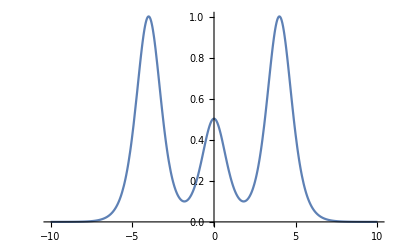

```mathematica
Plot[V1[x],{x,-10,10}]
```

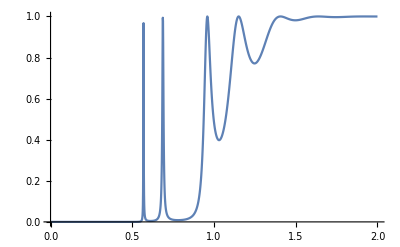

```mathematica
(*here we find the transmission coefficient from two points*)
T1[k0_]:=Module[{help=SchrEq1[k0]},(Exp[2Sqrt[2]I k0 a1]-Exp[2Sqrt[2]I k0 (a1-c1)])/(Exp[Sqrt[2]I k0 a1](f[a1]/.help)-Exp[Sqrt[2]I k0(a1-c1)](f[a1-c1]/.help))][[1]];

t1=Table[{k,Abs[T1[k]]^2},{k,0.001,2,0.001}];
lp1=ListPlot[t1,PlotRange->All,Joined->True];

Show[lp1]
```

## Packaging the above routines as a function of the potential

```mathematica
SEDict=Association["a"->-10, "b"->10, "c"->4];
```

```mathematica
SchrEqOfV[V_,VParams_,SEDict_,k_]:=Module[{a,b,c, sol},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];

sol = NDSolve[{-f''[x]/2+V[x, VParams]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}];
Return[sol];
];
```

```mathematica
VTest[x_,params_]:=Module[{a,b,c,pot},
(* Extract params*)
a=params[[1]];
b=params[[2]];
c=params[[3]];
(* Calculate potential *) 
pot = a/Cosh[(x-b)/c]^2;
Return[pot]
];
```

```mathematica
VParamsTest = {1,0,1};
```

```mathematica
func=(f/.SchrEqOfV[VTest, VParamsTest, SEDict,1][[1]])
```

InterpolatingFunction[{{-14., 10.}}, <>]

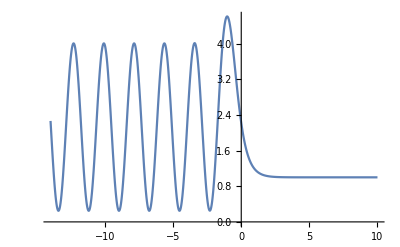

```mathematica
Plot[Abs[func[x]]^2,{x,-14,10}]
```

```mathematica
WaveFuncLeftOfV[V_, VParams_, SEDict_, k_,step_:1]:=Module[{a,b,c,help=SchrEqOfV[V,VParams,SEDict,k]},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];
Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k,a,step/k}],{Exp[I Sqrt[2]k x],Exp[-I Sqrt[2]k x]},x]
];
```

```mathematica
TofV[V_,VParams_, SEDict_,k_,step_:1]:=1/(WaveFuncLeftOfV[V, VParams,SEDict,k,step][[2]]/.x->0);
```

```mathematica
t=Table[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.01}];
lp=ListPlot[t,PlotRange->All];
```

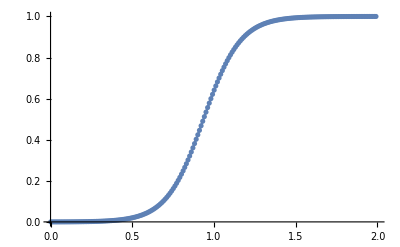

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

## Timing

```mathematica
res = ParallelTable[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.001}]//Timing;
```

```mathematica
res[[1]] (*seconds*)
```

0.119969

```mathematica
Length[res[[2]]]
```

2000

```mathematica
(*SE solutions per second*)
```

```mathematica
Length[res[[2]]]/res[[1]]
```

16671.

## TofKVec

```mathematica
getKVec[kmin_,kmax_,knum_]:=Table[k,{k,kmin,kmax,(kmax-kmin)/(knum-1)}]
```

```mathematica
TofVVec[V_,VParams_,SEDict_,kVec_]:=ParallelTable[{k,TofV[V, VParams, SEDict, k]},{k,kVec}]
```

```mathematica
kVecTest=getKVec[0.01,2,100];
```

## Cost

```mathematica
Cost[T_, TGoal_]:=
Module[{Tdiff, cost},
(*Calculate difference in vectors*)
Tdiff=Table[{T[[i,1]],Abs[T[[i,2]]-TGoal[[i,2]]]^2},{i,1,Length[T]}];

(*Calculate loss. Estimate integral using midpoint rule. Normalize by interval. *)
Throw[
cost = Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (Tdiff[[i,2]]+Tdiff[[i+1,2]]),{i,1,Length[T]-1}] / (T[[Length[T],1]]-T[[1,1]]),
Print[Length[T]]
];
Return[cost];
];
```

```mathematica
TGoalTest=Table[{x,Sqrt[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2)]},{x,kVecTest}];
```

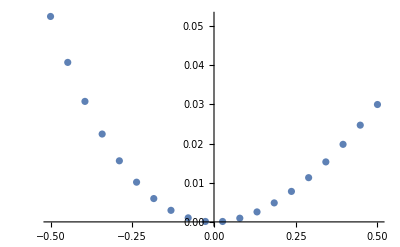

```mathematica
(* Plot the cost as a function of "a=1+eps", the coefficient of the Sech^2 potential. "eps=0" should reproduce the analytic results. *)
(* Getting lots of errors here, but the plot works fine. May have to worry more about these in the NMinimize routine. *)
ListPlot[Table[{eps,Cost[Abs[TofVVec[VTest,{1+eps,0,1},SEDict,kVecTest]],TGoalTest]},{eps,-0.5,0.5,1/19}]]
```

## Differential Evolution

```mathematica
(* Minimize the parameters of the potential to find the known solution. *)
```

```mathematica
(*NMinimize[{Hold[Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]],{v3>0}},{v1,v3}, 
Method->{"DifferentialEvolution", "Tolerance"->0.02}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:>Hold[Print["Params: ",{v1,0,v3} , " Cost: ", Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]]]]*)
```

## Gaussian Potential

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

{{-1,-0.5,0.7},{0.5,0.5,1.5}}

0.5 ⅇ^(-0.333333 (-0.5+x)^2)-ⅇ^(-0.714286 (0.5+x)^2)

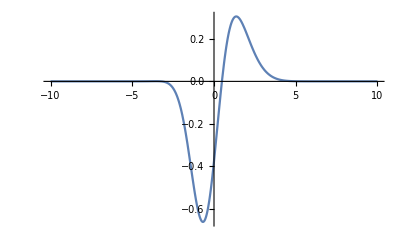

```mathematica
paramsTest = {{-1,-0.5,0.7},{0.5,0.5,1.5}}
VGaussN[x,paramsTest]
Plot[VGaussN[x,paramsTest],{x,a,b},PlotRange->All]
```

```mathematica
SEDict
```

<|a→-10,b→10,c→4|>

```mathematica
SchrEqOfV[VGaussN,paramsTest,SEDict,0.05]
```

```mathematica
TofV[VGaussN,paramsTest,SEDict,0.05]
```

0.00915094+0.039589 ⅈ

```mathematica
TofVVec[VGaussN,paramsTest,SEDict,{0.05}]
```

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

{{0.05,(2.23607+0. ⅈ)/((0.405306+0.00573209 ⅈ) f[-90.]+(0.141653+0.499672 ⅈ) f[-70.]-(0.361127-0.150109 ⅈ) f[-50.]-(0.254284+0.452855 ⅈ) f[-30.]+(0.281819-0.291349 ⅈ) f[-10.])}}

```mathematica
TofVVec[VGaussN,paramsTest,SEDict,kVecTest]
```

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

{{0.01,(2.23607+0. ⅈ)/((0.339096+0.222081 ⅈ) f[-410.]-(0.148235-0.497759 ⅈ) f[-310.]-(0.385329+0.0668364 ⅈ) f[-210.]+(0.0280561-0.518605 ⅈ) f[-110.]+(0.394079-0.0949099 ⅈ) f[-10.])},{0.030101,(2.23607+0. ⅈ)/((0.387771+0.118066 ⅈ) f[-142.886]-(0.00268545-0.519356 ⅈ) f[-109.664]-(0.388609-0.0439145 ⅈ) f[-76.443]-(0.118517+0.50566 ⅈ) f[-43.2215]+(0.351645-0.201623 ⅈ) f[-10.])},{0.050202,(2.23607+0. ⅈ)/((0.405321-0.00457411 ⅈ) f[-89.6781]+(0.14308-0.499266 ⅈ) f[-69.7586]-(0.360696+0.151141 ⅈ) f[-49.839]-(0.255577-0.452127 ⅈ) f[-29.9195]+(0.280985+0.292153 ⅈ) f[-10.])},{0.070303,(2.23607+0. ⅈ)/((0.390337+0.109285 ⅈ) f[-66.8966]+(0.277361-0.4391 ⅈ) f[-52.6724]-(0.303832+0.246235 ⅈ) f[-38.4483]-(0.372122-0.362303 ⅈ) f[-24.2241]+(0.187772+0.359233 ⅈ) f[-10.])},{0.090404,(2.23607+0. ⅈ)/((0.344021-0.214372 ⅈ) f[-54.2458]+(0.389378+0.34369 ⅈ) f[-43.1844]-(0.222579-0.321565 ⅈ) f[-32.1229]-(0.458798+0.243398 ⅈ) f[-21.0615]+(0.079486-0.397477 ⅈ) f[-10.])},{0.110505,(2.23607+0. ⅈ)/((0.270092+0.302252 ⅈ) f[-46.1974]+(0.470142-0.220692 ⅈ) f[-37.1481]-(0.123461+0.371083 ⅈ) f[-28.0987]-(0.508647-0.104956 ⅈ) f[-19.0494]-(0.0351797-0.403818 ⅈ) f[-10.])},{0.130606,(2.23607+0. ⅈ)/((0.174483-0.365871 ⅈ) f[-40.6265]+(0.513168+0.0799797 ⅈ) f[-32.9698]-(0.0144328-0.390816 ⅈ) f[-25.3132]-(0.517669-0.0419109 ⅈ) f[-17.6566]-(0.147022+0.377744 ⅈ) f[-10.])},{0.150707,(2.23607+0. ⅈ)/((0.0648692+0.400123 ⅈ) f[-36.5416]+(0.515003+0.0671522 ⅈ) f[-29.9062]+(0.0957538-0.379179 ⅈ) f[-23.2708]-(0.485139+0.185413 ⅈ) f[-16.6354]-(0.247063-0.321351 ⅈ) f[-10.])},{0.170808,(2.23607+0. ⅈ)/((-0.0499518-0.402257 ⅈ) f[-33.4181]+(0.475501-0.208894 ⅈ) f[-27.5636]+(0.198255+0.337106 ⅈ) f[-21.709]-(0.413668-0.314033 ⅈ) f[-15.8545]-(0.327272+0.239163 ⅈ) f[-10.])},{0.190909,(2.23607+0. ⅈ)/((-0.160763-0.372104 ⅈ) f[-30.9524]+(0.397831-0.333868 ⅈ) f[-25.7143]+(0.284842+0.267975 ⅈ) f[-20.4762]-(0.308993-0.417446 ⅈ) f[-15.2381]-(0.381213+0.137778 ⅈ) f[-10.])},{0.21101,(2.23607+0. ⅈ)/((-0.258671-0.312083 ⅈ) f[-28.9564]+(0.288229-0.432044 ⅈ) f[-24.2173]+(0.348566+0.177334 ⅈ) f[-19.4782]-(0.179516-0.487352 ⅈ) f[-14.7391]-(0.404555+0.0253346 ⅈ) f[-10.])},{0.231111,(2.23607+0. ⅈ)/((-0.335816-0.227011 ⅈ) f[-27.3077]+(0.155491-0.495541 ⅈ) f[-22.9808]+(0.384311+0.0724585 ⅈ) f[-18.6538]-(0.0356293-0.518139 ⅈ) f[-14.3269]-(0.395424-0.0891427 ⅈ) f[-10.])},{0.251212,(2.23607+0. ⅈ)/((-0.386005+0.123718 ⅈ) f[-25.9228]+(0.0102723+0.519261 ⅈ) f[-21.9421]+(0.389209+0.0382327 ⅈ) f[-17.9614]+(0.111117-0.507337 ⅈ) f[-13.9807]-(0.354553+0.196465 ⅈ) f[-10.])},{0.271313,(2.23607+0. ⅈ)/((-0.405211+0.0104949 ⅈ) f[-24.7431]-(0.135771-0.501303 ⅈ) f[-21.0573]+(0.362866+0.145855 ⅈ) f[-17.3716]+(0.248944-0.455812 ⅈ) f[-13.6858]-(0.285223+0.288017 ⅈ) f[-10.])},{0.291414,(2.23607+0. ⅈ)/((-0.391892-0.103571 ⅈ) f[-23.7262]-(0.270916-0.443105 ⅈ) f[-20.2946]+(0.307397+0.24177 ⅈ) f[-16.8631]+(0.366789-0.3677 ⅈ) f[-13.4315]-(0.193+0.356451 ⅈ) f[-10.])},{0.311515,(2.23607+0. ⅈ)/((-0.347116-0.209324 ⅈ) f[-22.8405]-(0.384316-0.349341 ⅈ) f[-19.6304]+(0.227253+0.318279 ⅈ) f[-16.4202]+(0.455193-0.250074 ⅈ) f[-13.2101]-(0.0852842+0.396274 ⅈ) f[-10.])},{0.331616,(2.23607+0. ⅈ)/((-0.274479-0.298274 ⅈ) f[-22.0621]-(0.466867-0.227536 ⅈ) f[-19.0466]+(0.128869+0.36924 ⅈ) f[-16.0311]+(0.50706-0.112375 ⅈ) f[-13.0155]+(0.0292767-0.404288 ⅈ) f[-10.])},{0.351717,(2.23607+0. ⅈ)/((-0.17981+0.363283 ⅈ) f[-21.3728]-(0.511945+0.0874679 ⅈ) f[-18.5296]+(0.0201406-0.390563 ⅈ) f[-15.6864]+(0.518226-0.0343439 ⅈ) f[-12.8432]+(0.141488+0.379852 ⅈ) f[-10.])},{0.371818,(2.23607+0. ⅈ)/((-0.0707076+0.399132 ⅈ) f[-20.7579]-(0.515929-0.0596215 ⅈ) f[-18.0685]-(0.0902043+0.380537 ⅈ) f[-15.379]+(0.487796-0.178306 ⅈ) f[-12.6895]+(0.242342+0.324926 ⅈ) f[-10.])},{0.391919,(2.23607+0. ⅈ)/((0.04407-0.402944 ⅈ) f[-20.2062]-(0.478502+0.201925 ⅈ) f[-17.6546]-(0.193309-0.339966 ⅈ) f[-15.1031]+(0.418211+0.307956 ⅈ) f[-12.5515]+(0.323744-0.243919 ⅈ) f[-10.])},{0.41202,(2.23607+0. ⅈ)/((0.15531+0.374413 ⅈ) f[-19.7083]-(0.402666-0.328021 ⅈ) f[-17.2812]-(0.280897+0.272107 ⅈ) f[-14.8541]+(0.315058-0.412888 ⅈ) f[-12.4271]+(0.379159+0.143333 ⅈ) f[-10.])},{0.432121,(2.23607+0. ⅈ)/((0.254084-0.315828 ⅈ) f[-19.2567]-(0.29451+0.427787 ⅈ) f[-16.9425]-(0.345938-0.182407 ⅈ) f[-14.6283]+(0.186616+0.484678 ⅈ) f[-12.3142]+(0.404141-0.031242 ⅈ) f[-10.])},{0.452222,(2.23607+0. ⅈ)/((0.332463+0.231893 ⅈ) f[-18.8452]-(0.162714-0.493216 ⅈ) f[-16.6339]-(0.383212+0.0780651 ⅈ) f[-14.4226]+(0.0431949-0.517564 ⅈ) f[-12.2113]+(0.396684-0.0833565 ⅈ) f[-10.])},{0.472323,(2.23607+0. ⅈ)/((0.384157+0.129344 ⅈ) f[-18.4688]-(0.017857-0.519056 ⅈ) f[-16.3516]-(0.389726-0.0325428 ⅈ) f[-14.2344]-(0.103694+0.508906 ⅈ) f[-12.1172]+(0.357385-0.191264 ⅈ) f[-10.])},{0.492424,(2.23607+0. ⅈ)/((0.405015-0.0164134 ⅈ) f[-18.1231]+(0.128433-0.503232 ⅈ) f[-16.0923]-(0.364958+0.140538 ⅈ) f[-14.0615]-(0.242259-0.4594 ⅈ) f[-12.0308]+(0.2894+0.28382 ⅈ) f[-10.])},{0.512525,(2.23607+0. ⅈ)/((0.393363+0.0978349 ⅈ) f[-17.8045]+(0.264414-0.447016 ⅈ) f[-15.8534]-(0.310896+0.237253 ⅈ) f[-13.9022]-(0.361379-0.373019 ⅈ) f[-11.9511]+(0.198186+0.353594 ⅈ) f[-10.])},{0.532626,(2.23607+0. ⅈ)/((0.350137-0.20423 ⅈ) f[-17.51]+(0.379171+0.354918 ⅈ) f[-15.6325]-(0.231879-0.314925 ⅈ) f[-13.755]-(0.451491+0.256697 ⅈ) f[-11.8775]+(0.0910642-0.394985 ⅈ) f[-10.])},{0.552727,(2.23607+0. ⅈ)/((0.278807-0.294233 ⅈ) f[-17.2368]+(0.463493+0.234333 ⅈ) f[-15.4276]-(0.134249-0.367318 ⅈ) f[-13.6184]-(0.505364+0.119771 ⅈ) f[-11.8092]-(0.0233674+0.404673 ⅈ) f[-10.])},{0.572828,(2.23607+0. ⅈ)/((0.185098-0.360618 ⅈ) f[-16.9829]+(0.510612+0.0949375 ⅈ) f[-15.2372]-(0.0258442-0.390227 ⅈ) f[-13.4914]-(0.518673-0.0267695 ⅈ) f[-11.7457]-(0.135923+0.381878 ⅈ) f[-10.])},{0.592929,(2.23607+0. ⅈ)/((0.0765309+0.398057 ⅈ) f[-16.7462]+(0.516745+0.052078 ⅈ) f[-15.0596]+(0.0846354-0.381814 ⅈ) f[-13.3731]-(0.490349+0.171161 ⅈ) f[-11.6865]-(0.237569-0.328431 ⅈ) f[-10.])},{0.61303,(2.23607+0. ⅈ)/((-0.0381787-0.403545 ⅈ) f[-16.525]+(0.481401-0.194913 ⅈ) f[-14.8937]+(0.188322+0.342754 ⅈ) f[-13.2625]-(0.422666-0.301814 ⅈ) f[-11.6312]-(0.320146+0.248622 ⅈ) f[-10.])},{0.633131,(2.23607+0. ⅈ)/((-0.149824-0.376642 ⅈ) f[-16.3178]+(0.407415-0.322103 ⅈ) f[-14.7384]+(0.276892+0.276182 ⅈ) f[-13.1589]-(0.321056-0.408241 ⅈ) f[-11.5795]-(0.377025+0.148857 ⅈ) f[-10.])},{0.653232,(2.23607+0. ⅈ)/((-0.249443-0.319506 ⅈ) f[-16.1234]+(0.300728-0.423439 ⅈ) f[-14.5925]+(0.343236+0.187441 ⅈ) f[-13.0617]-(0.193677-0.4819 ⅈ) f[-11.5308]-(0.403642+0.0371427 ⅈ) f[-10.])},{0.673333,(2.23607+0. ⅈ)/((-0.32904-0.236725 ⅈ) f[-15.9406]+(0.169902-0.490786 ⅈ) f[-14.4554]+(0.38203+0.083655 ⅈ) f[-12.9703]-(0.0507512-0.516877 ⅈ) f[-11.4851]-(0.397859-0.0775526 ⅈ) f[-10.])},{0.693434,(2.23607+0. ⅈ)/((-0.382226+0.134943 ⅈ) f[-15.7684]+(0.0254379+0.51874 ⅈ) f[-14.3263]+(0.39016+0.0268458 ⅈ) f[-12.8842]+(0.096248-0.510367 ⅈ) f[-11.4421]-(0.360141+0.186023 ⅈ) f[-10.])},{0.713535,(2.23607+0. ⅈ)/((-0.404732+0.0223284 ⅈ) f[-15.6059]-(0.121068-0.505055 ⅈ) f[-14.2044]+(0.366972+0.135192 ⅈ) f[-12.8029]+(0.235522-0.46289 ⅈ) f[-11.4015]-(0.293516+0.279562 ⅈ) f[-10.])},{0.733636,(2.23607+0. ⅈ)/((-0.39475-0.0920779 ⅈ) f[-15.4523]-(0.257856-0.450831 ⅈ) f[-14.0892]+(0.314328+0.232686 ⅈ) f[-12.7261]+(0.355891-0.378259 ⅈ) f[-11.3631]-(0.203331+0.350661 ⅈ) f[-10.])},{0.753737,(2.23607+0. ⅈ)/((-0.353084+0.199093 ⅈ) f[-15.3069]-(0.373946+0.36042 ⅈ) f[-13.9802]+(0.236455-0.311504 ⅈ) f[-12.6534]+(0.447693+0.263266 ⅈ) f[-11.3267]-(0.0968247-0.393613 ⅈ) f[-10.])},{0.773838,(2.23607+0. ⅈ)/((-0.283076-0.290128 ⅈ) f[-15.169]-(0.460021-0.241079 ⅈ) f[-13.8768]+(0.139601+0.365318 ⅈ) f[-12.5845]+(0.503561-0.127141 ⅈ) f[-11.2923]+(0.0174531-0.404971 ⅈ) f[-10.])},{0.793939,(2.23607+0. ⅈ)/((-0.190346-0.357875 ⅈ) f[-15.0382]-(0.509171-0.102387 ⅈ) f[-13.7786]+(0.0315422+0.389808 ⅈ) f[-12.5191]+(0.519008+0.0191895 ⅈ) f[-11.2595]+(0.13033-0.383823 ⅈ) f[-10.])},{0.81404,(2.23607+0. ⅈ)/((-0.0823379+0.396896 ⅈ) f[-14.9138]-(0.517451-0.0445234 ⅈ) f[-13.6853]-(0.0790486+0.38301 ⅈ) f[-12.4569]+(0.492797-0.163979 ⅈ) f[-11.2284]+(0.232746+0.331867 ⅈ) f[-10.])},{0.834141,(2.23607+0. ⅈ)/((0.0322793-0.40406 ⅈ) f[-14.7953]-(0.484197+0.18786 ⅈ) f[-13.5965]-(0.183294-0.345469 ⅈ) f[-12.3977]+(0.42703+0.295607 ⅈ) f[-11.1988]+(0.316479-0.253272 ⅈ) f[-10.])},{0.854242,(2.23607+0. ⅈ)/((0.144306-0.37879 ⅈ) f[-14.6825]-(0.412078+0.316117 ⅈ) f[-13.5119]-(0.272827-0.280197 ⅈ) f[-12.3413]+(0.326986+0.403507 ⅈ) f[-11.1706]+(0.37481-0.154349 ⅈ) f[-10.])},{0.874343,(2.23607+0. ⅈ)/((0.244749+0.323116 ⅈ) f[-14.5749]-(0.306882-0.419001 ⅈ) f[-13.4311]-(0.340461+0.192435 ⅈ) f[-12.2874]+(0.200696-0.479019 ⅈ) f[-11.1437]+(0.403056+0.0430354 ⅈ) f[-10.])},{0.894444,(2.23607+0. ⅈ)/((0.325547-0.241507 ⅈ) f[-14.472]-(0.177053+0.488252 ⅈ) f[-13.354]-(0.380767-0.0892271 ⅈ) f[-12.236]+(0.0582968+0.516081 ⅈ) f[-11.118]+(0.39895+0.071732 ⅈ) f[-10.])},{0.914545,(2.23607+0. ⅈ)/((0.380214+0.140512 ⅈ) f[-14.3738]-(0.0330134-0.518313 ⅈ) f[-13.2803]-(0.39051-0.0211432 ⅈ) f[-12.1869]-(0.0887819+0.511718 ⅈ) f[-11.0934]+(0.36282-0.180742 ⅈ) f[-10.])},{0.934646,(2.23607+0. ⅈ)/((0.404362+0.0282387 ⅈ) f[-14.2797]+(0.113677+0.50677 ⅈ) f[-13.2098]-(0.368908-0.129816 ⅈ) f[-12.1398]-(0.228734+0.466282 ⅈ) f[-11.0699]+(0.297569-0.275244 ⅈ) f[-10.])},{0.954747,(2.23607+0. ⅈ)/((0.396053-0.0863012 ⅈ) f[-14.1896]+(0.251242+0.45455 ⅈ) f[-13.1422]-(0.317694-0.22807 ⅈ) f[-12.0948]-(0.350327+0.383418 ⅈ) f[-11.0474]+(0.208432-0.347653 ⅈ) f[-10.])},{0.974848,(2.23607+0. ⅈ)/((0.355954-0.193914 ⅈ) f[-14.1032]+(0.368641+0.365844 ⅈ) f[-13.0774]-(0.24098-0.308016 ⅈ) f[-12.0516]-(0.443799+0.269778 ⅈ) f[-11.0258]+(0.102565-0.392156 ⅈ) f[-10.])},{0.994949,(2.23607+0. ⅈ)/((0.287284-0.285962 ⅈ) f[-14.0203]+(0.45645+0.247773 ⅈ) f[-13.0152]-(0.144923-0.363239 ⅈ) f[-12.0102]-(0.501649+0.134484 ⅈ) f[-11.0051]-(0.0115351+0.405183 ⅈ) f[-10.])},{1.01505,(2.23607+0. ⅈ)/((0.195554-0.355056 ⅈ) f[-13.9407]+(0.507621+0.109814 ⅈ) f[-12.9555]-(0.0372334-0.389306 ⅈ) f[-11.9703]-(0.519233-0.0116053 ⅈ) f[-10.9852]-(0.124709+0.385686 ⅈ) f[-10.])},{1.03515,(2.23607+0. ⅈ)/((0.0881273-0.395651 ⅈ) f[-13.8642]+(0.518046-0.0369593 ⅈ) f[-12.8981]+(0.0734448+0.384124 ⅈ) f[-11.9321]-(0.49514-0.156763 ⅈ) f[-10.966]-(0.227873+0.335232 ⅈ) f[-10.])},{1.05525,(2.23607+0. ⅈ)/((-0.0263731+0.404488 ⅈ) f[-13.7906]+(0.48689+0.180766 ⅈ) f[-12.8429]+(0.178228-0.348109 ⅈ) f[-11.8953]-(0.431303+0.289337 ⅈ) f[-10.9476]-(0.312746-0.257869 ⅈ) f[-10.])},{1.07535,(2.23607+0. ⅈ)/((-0.138757-0.380858 ⅈ) f[-13.7197]+(0.416652-0.310063 ⅈ) f[-12.7898]+(0.268705+0.284153 ⅈ) f[-11.8599]-(0.332846-0.398687 ⅈ) f[-10.9299]-(0.372515+0.159808 ⅈ) f[-10.])},{1.09545,(2.23607+0. ⅈ)/((-0.240002+0.326657 ⅈ) f[-13.6515]+(0.31297+0.414473 ⅈ) f[-12.7386]+(0.337614-0.197389 ⅈ) f[-11.8257]-(0.207673+0.476036 ⅈ) f[-10.9129]-(0.402384-0.048919 ⅈ) f[-10.])},{1.11556,(2.23607+0. ⅈ)/((-0.321984+0.246237 ⅈ) f[-13.5857]+(0.184167+0.485613 ⅈ) f[-12.6892]+(0.379423-0.0947801 ⅈ) f[-11.7928]-(0.0658299+0.515174 ⅈ) f[-10.8964]-(0.399955+0.0658962 ⅈ) f[-10.])},{1.13566,(2.23607+0. ⅈ)/((-0.378121-0.146051 ⅈ) f[-13.5222]+(0.0405818-0.517775 ⅈ) f[-12.6416]+(0.390778-0.0154361 ⅈ) f[-11.7611]+(0.0812968+0.512961 ⅈ) f[-10.8805]-(0.365422-0.175422 ⅈ) f[-10.])},{1.15576,(2.23607+0. ⅈ)/((-0.403906-0.0341429 ⅈ) f[-13.4609]-(0.106261+0.508376 ⅈ) f[-12.5957]+(0.370765-0.124413 ⅈ) f[-11.7305]+(0.221898+0.469573 ⅈ) f[-10.8652]-(0.301558-0.270867 ⅈ) f[-10.])},{1.17586,(2.23607+0. ⅈ)/((-0.397272+0.0805061 ⅈ) f[-13.4018]-(0.244575+0.458172 ⅈ) f[-12.5513]+(0.320992-0.223404 ⅈ) f[-11.7009]+(0.344688+0.388495 ⅈ) f[-10.8504]-(0.213488-0.344571 ⅈ) f[-10.])},{1.19596,(2.23607+0. ⅈ)/((-0.358749+0.188693 ⅈ) f[-13.3446]-(0.363257+0.371191 ⅈ) f[-12.5084]+(0.245454-0.304463 ⅈ) f[-11.6723]+(0.439811+0.276232 ⅈ) f[-10.8361]-(0.108283-0.390616 ⅈ) f[-10.])},{1.21606,(2.23607+0. ⅈ)/((-0.291431-0.281734 ⅈ) f[-13.2893]-(0.452781-0.254415 ⅈ) f[-12.467]+(0.150214+0.361083 ⅈ) f[-11.6447]+(0.499631-0.141798 ⅈ) f[-10.8223]+(0.00561461-0.405308 ⅈ) f[-10.])},{1.23616,(2.23607+0. ⅈ)/((-0.20072-0.352161 ⅈ) f[-13.2358]-(0.505962-0.117218 ⅈ) f[-12.4269]+(0.0429168+0.38872 ⅈ) f[-11.6179]+(0.519347+0.0040187 ⅈ) f[-10.809]+(0.119061-0.387467 ⅈ) f[-10.])},{1.25626,(2.23607+0. ⅈ)/((-0.0938979+0.394321 ⅈ) f[-13.184]-(0.518531-0.0293873 ⅈ) f[-12.388]-(0.0678254+0.385156 ⅈ) f[-11.592]+(0.497377-0.149513 ⅈ) f[-10.796]+(0.222951+0.338525 ⅈ) f[-10.])},{1.27636,(2.23607+0. ⅈ)/((0.0204612+0.40483 ⅈ) f[-13.1339]-(0.489478-0.173634 ⅈ) f[-12.3504]-(0.173123+0.350676 ⅈ) f[-11.567]+(0.435483-0.283005 ⅈ) f[-10.7835]+(0.308945+0.26241 ⅈ) f[-10.])},{1.29646,(2.23607+0. ⅈ)/((0.133178+0.382844 ⅈ) f[-13.0853]-(0.421137-0.303944 ⅈ) f[-12.314]-(0.264525+0.288048 ⅈ) f[-11.5427]+(0.338635-0.393782 ⅈ) f[-10.7713]+(0.370141+0.165233 ⅈ) f[-10.])},{1.31657,(2.23607+0. ⅈ)/((0.235205+0.330129 ⅈ) f[-13.0382]-(0.318992-0.409856 ⅈ) f[-12.2787]-(0.334694+0.2023 ⅈ) f[-11.5191]+(0.214605-0.472951 ⅈ) f[-10.7596]+(0.401627+0.0547921 ⅈ) f[-10.])},{1.33667,(2.23607+0. ⅈ)/((0.318352+0.250914 ⅈ) f[-12.9925]-(0.191242-0.482871 ⅈ) f[-12.2444]-(0.377998+0.100313 ⅈ) f[-11.4963]+(0.073349-0.514157 ⅈ) f[-10.7481]+(0.400875-0.0600463 ⅈ) f[-10.])},{1.35677,(2.23607+0. ⅈ)/((0.375947+0.15156 ⅈ) f[-12.9482]-(0.0481415-0.517127 ⅈ) f[-12.2111]-(0.390961-0.00972562 ⅈ) f[-11.4741]-(0.0737944+0.514094 ⅈ) f[-10.737]+(0.367946-0.170065 ⅈ) f[-10.])},{1.37687,(2.23607+0. ⅈ)/((0.403365-0.0400399 ⅈ) f[-12.9051]+(0.098823-0.509874 ⅈ) f[-12.1789]-(0.372543+0.118984 ⅈ) f[-11.4526]-(0.215014-0.472765 ⅈ) f[-10.7263]+(0.305483+0.266433 ⅈ) f[-10.])},{1.39697,(2.23607+0. ⅈ)/((0.398406-0.0746939 ⅈ) f[-12.8633]+(0.237855+0.461696 ⅈ) f[-12.1475]-(0.324222-0.218691 ⅈ) f[-11.4317]-(0.338976+0.393489 ⅈ) f[-10.7158]+(0.218499-0.341415 ⅈ) f[-10.])},{1.41707,(2.23607+0. ⅈ)/((0.361468-0.183432 ⅈ) f[-12.8227]+(0.357795+0.376458 ⅈ) f[-12.117]-(0.249876-0.300845 ⅈ) f[-11.4114]-(0.435729+0.282628 ⅈ) f[-10.7057]+(0.113978-0.388993 ⅈ) f[-10.])},{1.43717,(2.23607+0. ⅈ)/((0.295516-0.277447 ⅈ) f[-12.7832]+(0.449016+0.261002 ⅈ) f[-12.0874]-(0.155473-0.35885 ⅈ) f[-11.3916]-(0.497506+0.149082 ⅈ) f[-10.6958]+(0.000307059-0.405347 ⅈ) f[-10.])},{1.45727,(2.23607+0. ⅈ)/((0.205843-0.349192 ⅈ) f[-12.7449]+(0.504196+0.124597 ⅈ) f[-12.0586]-(0.0485909-0.388052 ⅈ) f[-11.3724]-(0.519351+0.00356878 ⅈ) f[-10.6862]-(0.113388+0.389165 ⅈ) f[-10.])},{1.47737,(2.23607+0. ⅈ)/((0.0996484-0.392908 ⅈ) f[-12.7075]+(0.518905-0.021809 ⅈ) f[-12.0306]+(0.0621915+0.386106 ⅈ) f[-11.3538]-(0.499508-0.142231 ⅈ) f[-10.6769]-(0.217982+0.341746 ⅈ) f[-10.])},{1.49747,(2.23607+0. ⅈ)/((-0.0145449-0.405086 ⅈ) f[-12.6712]+(0.491963-0.166465 ⅈ) f[-12.0034]+(0.167982+0.353168 ⅈ) f[-11.3356]-(0.439571-0.276613 ⅈ) f[-10.6678]-(0.305079+0.266895 ⅈ) f[-10.])},{1.51758,(2.23607+0. ⅈ)/((-0.127571+0.384749 ⅈ) f[-12.6358]+(0.425532+0.297759 ⅈ) f[-11.9768]+(0.260289-0.291882 ⅈ) f[-11.3179]-(0.344351+0.388793 ⅈ) f[-10.6589]-(0.367688-0.170622 ⅈ) f[-10.])},{1.53768,(2.23607+0. ⅈ)/((-0.230357-0.333529 ⅈ) f[-12.6013]+(0.324945-0.405153 ⅈ) f[-11.951]+(0.331703+0.207168 ⅈ) f[-11.3007]-(0.221491-0.469766 ⅈ) f[-10.6503]-(0.400783+0.0606536 ⅈ) f[-10.])},{1.55778,(2.23607+0. ⅈ)/((-0.314653-0.255538 ⅈ) f[-12.5678]+(0.198276-0.480026 ⅈ) f[-11.9258]+(0.376492+0.105824 ⅈ) f[-11.2839]-(0.0808524-0.513031 ⅈ) f[-10.6419]-(0.401709-0.0541836 ⅈ) f[-10.])},{1.57788,(2.23607+0. ⅈ)/((-0.373692-0.157036 ⅈ) f[-12.535]+(0.055691-0.516369 ⅈ) f[-11.9013]+(0.391062-0.0040131 ⅈ) f[-11.2675]+(0.0662762+0.515117 ⅈ) f[-10.6338]-(0.370391-0.164672 ⅈ) f[-10.])},{1.59798,(2.23607+0. ⅈ)/((-0.402737-0.0459283 ⅈ) f[-12.5032]-(0.0913638+0.511264 ⅈ) f[-11.8774]+(0.374241-0.113528 ⅈ) f[-11.2516]+(0.208085+0.475856 ⅈ) f[-10.6258]-(0.309342-0.261942 ⅈ) f[-10.])},{1.61808,(2.23607+0. ⅈ)/((-0.399454-0.0688657 ⅈ) f[-12.4721]-(0.231085-0.465121 ⅈ) f[-11.854]+(0.327382+0.213931 ⅈ) f[-11.236]+(0.333191-0.398399 ⅈ) f[-10.618]-(0.223464+0.338187 ⅈ) f[-10.])},{1.63818,(2.23607+0. ⅈ)/((-0.364109-0.178132 ⅈ) f[-12.4417]-(0.352258-0.381644 ⅈ) f[-11.8313]+(0.254244+0.297162 ⅈ) f[-11.2209]+(0.431553-0.288963 ⅈ) f[-10.6104]-(0.119648+0.387286 ⅈ) f[-10.])},{1.65828,(2.23607+0. ⅈ)/((-0.299537-0.2731 ⅈ) f[-12.4121]-(0.445155-0.267534 ⅈ) f[-11.8091]+(0.160699+0.356541 ⅈ) f[-11.2061]+(0.495275-0.156334 ⅈ) f[-10.603]-(0.00622866+0.405299 ⅈ) f[-10.])},{1.67838,(2.23607+0. ⅈ)/((-0.210923+0.346147 ⅈ) f[-12.3832]-(0.502322+0.13195 ⅈ) f[-11.7874]+(0.0542547-0.387301 ⅈ) f[-11.1916]+(0.519243+0.0111555 ⅈ) f[-10.5958]+(0.107691+0.39078 ⅈ) f[-10.])},{1.69848,(2.23607+0. ⅈ)/((-0.105378+0.39141 ⅈ) f[-12.355]-(0.519168-0.0142261 ⅈ) f[-11.7663]-(0.0565443+0.386973 ⅈ) f[-11.1775]+(0.501533-0.134918 ⅈ) f[-10.5888]+(0.212966+0.344894 ⅈ) f[-10.])},{1.71859,(2.23607+0. ⅈ)/((0.00862552-0.405255 ⅈ) f[-12.3275]-(0.494342+0.15926 ⅈ) f[-11.7456]-(0.162805-0.355584 ⅈ) f[-11.1637]+(0.443565+0.270162 ⅈ) f[-10.5819]+(0.301147-0.271324 ⅈ) f[-10.])},{1.73869,(2.23607+0. ⅈ)/((0.121936+0.386572 ⅈ) f[-12.3006]-(0.429837-0.291511 ⅈ) f[-11.7254]-(0.255997+0.295653 ⅈ) f[-11.1503]+(0.349994-0.383721 ⅈ) f[-10.5751]+(0.365156+0.175976 ⅈ) f[-10.])},{1.75879,(2.23607+0. ⅈ)/((0.22546-0.336859 ⅈ) f[-12.2743]-(0.330829+0.400362 ⅈ) f[-11.7057]-(0.328641-0.211991 ⅈ) f[-11.1371]+(0.22833+0.46648 ⅈ) f[-10.5686]+(0.399855-0.0665021 ⅈ) f[-10.])},{1.77889,(2.23607+0. ⅈ)/((0.310886+0.260108 ⅈ) f[-12.2486]-(0.205267-0.477078 ⅈ) f[-11.6864]-(0.374906+0.111313 ⅈ) f[-11.1243]+(0.0883385-0.511795 ⅈ) f[-10.5621]+(0.402458-0.0483093 ⅈ) f[-10.])},{1.79899,(2.23607+0. ⅈ)/((0.371358-0.162478 ⅈ) f[-12.2235]-(0.0632286+0.5155 ⅈ) f[-11.6676]-(0.391079-0.00170027 ⅈ) f[-11.1117]-(0.0587439-0.51603 ⅈ) f[-10.5559]+(0.372757+0.159243 ⅈ) f[-10.])},{1.81909,(2.23607+0. ⅈ)/((0.402023+0.0518069 ⅈ) f[-12.1989]+(0.083885+0.512544 ⅈ) f[-11.6492]-(0.37586-0.108049 ⅈ) f[-11.0995]-(0.201111+0.478845 ⅈ) f[-10.5497]+(0.313136-0.257395 ⅈ) f[-10.])},{1.83919,(2.23607+0. ⅈ)/((0.400418+0.0630228 ⅈ) f[-12.1749]+(0.224265-0.468447 ⅈ) f[-11.6312]-(0.330472+0.209126 ⅈ) f[-11.0874]-(0.327336-0.403224 ⅈ) f[-10.5437]+(0.22838+0.334886 ⅈ) f[-10.])},{1.85929,(2.23607+0. ⅈ)/((0.366672-0.172794 ⅈ) f[-12.1514]+(0.346645+0.38675 ⅈ) f[-11.6135]-(0.258558-0.293416 ⅈ) f[-11.0757]-(0.427286+0.295237 ⅈ) f[-10.5378]+(0.125293-0.385497 ⅈ) f[-10.])},{1.87939,(2.23607+0. ⅈ)/((0.303495+0.268695 ⅈ) f[-12.1283]+(0.4412-0.274009 ⅈ) f[-11.5963]-(0.16589+0.354155 ⅈ) f[-11.0642]-(0.492939-0.163552 ⅈ) f[-10.5321]+(0.0121489+0.405165 ⅈ) f[-10.])},{1.89949,(2.23607+0. ⅈ)/((0.215957+0.343029 ⅈ) f[-12.1058]+(0.500341-0.139274 ⅈ) f[-11.5794]-(0.0599069+0.386467 ⅈ) f[-11.0529]-(0.519025-0.0187398 ⅈ) f[-10.5265]-(0.10197-0.392311 ⅈ) f[-10.])},{1.9196,(2.23607+0. ⅈ)/((0.111085-0.389829 ⅈ) f[-12.0838]+(0.519321-0.00664018 ⅈ) f[-11.5628]+(0.050885+0.387758 ⅈ) f[-11.0419]-(0.50345-0.127577 ⅈ) f[-10.5209]-(0.207905+0.347968 ⅈ) f[-10.])},{1.9397,(2.23607+0. ⅈ)/((-0.0027043+0.405338 ⅈ) f[-12.0622]+(0.496616+0.152021 ⅈ) f[-11.5466]+(0.157593-0.357924 ⅈ) f[-11.0311]-(0.447465+0.263653 ⅈ) f[-10.5155]-(0.297151-0.275694 ⅈ) f[-10.])},{1.9598,(2.23607+0. ⅈ)/((-0.116276+0.388312 ⅈ) f[-12.041]+(0.434049+0.2852 ⅈ) f[-11.5308]+(0.251651-0.299362 ⅈ) f[-11.0205]-(0.355563+0.378567 ⅈ) f[-10.5103]-(0.362546-0.181291 ⅈ) f[-10.])},{1.9799,(2.23607+0. ⅈ)/((-0.220515+0.340117 ⅈ) f[-12.0203]+(0.336643+0.395487 ⅈ) f[-11.5152]+(0.325509-0.21677 ⅈ) f[-11.0102]-(0.235121+0.463094 ⅈ) f[-10.5051]-(0.39884-0.0723364 ⅈ) f[-10.])},{2.,(2.23607+0. ⅈ)/((-0.307053+0.264622 ⅈ) f[-12.]+(0.212215+0.474028 ⅈ) f[-11.5]+(0.37324-0.116778 ⅈ) f[-11.]-(0.0958058+0.51045 ⅈ) f[-10.5]-(0.403121+0.0424247 ⅈ) f[-10.])}}

```mathematica
Cost[Abs[TofVVec[VGaussN, paramsTest,SEDict,kVecTest]], TGoalTest]
```

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

Part::partw: Part 3 of {{-1,-0.5,0.7},{0.5,0.5,1.5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

100

Throw::nocatch: Uncaught … returned to top level.

Hold[Throw[0.502513 (0.0100505 (Abs[-0.998022+2.23607/Abs[(-0.314653-0.255538 ⅈ) f[-12.5678]+6]]^2+Abs[-0.997637+2.23607/Abs[(-0.230357-0.333529 ⅈ) f[-12.6013]+6]]^2)+0.0100505 (Abs[-0.897535+2.23607/Abs[1]]^2+Abs[-0.912158+2.23607/Abs[1]]^2)+0.0100505 (1^2+1^2)+93+1+0.0100505 (Abs[-0.0261193+17/1]^2+Abs[-0.0225783+1]^2)+0.0100505 (Abs[-0.0192165+2.23607/Abs[1]]^2+Abs[-0.0225783+2.23607/Abs[1]]^2)),Null]]
 |  |  |  |

```mathematica
NMinimize[{
Hold[Cost[Abs[TofVVec[VGaussN[x,{{A1,x01,sigma1},{A2,x02,sigma2}}],SEDict,kVecTest]], TGoalTest]],
{sigma1>0.01,sigma2>0.01,x01+x02==0}
},
{A1,x01,sigma1,A2,x02,sigma2}, 
Method->{"DifferentialEvolution", "Tolerance"->0.001}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:> Hold[Print["Params: ",{A1,x01,sigma1,A2,x02,sigma2} , " Cost: ", Cost[Abs[TofVVec[VGaussN[x,{{A1,x01,sigma1},{A2,x02,sigma2}}],SEDict,kVecTest]], TGoalTest]]]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

1

Throw::nocatch: Uncaught Throw[Indeterminate,Null] returned to top level.

Hold[Throw[Indeterminate,Null]]